## 5

```mathematica
Integrate[1/(8 Pi)Exp[-r],{r,Infinity,0}]
%//N
```

-1/(8 π)

-0.0397887

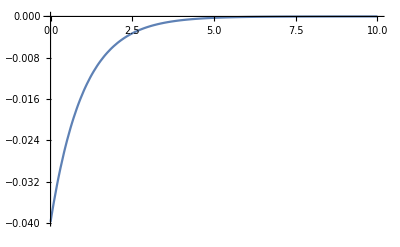

```mathematica
Plot [NIntegrate[1/(8 Pi)Exp[-r],{r,Infinity,x}],{x,0,10},PlotRange->All]
```

### Substitution

```mathematica
D[x/(x-1)^2,x]//Simplify
```

-(1+x)/(-1+x)^3

```mathematica
Integrate[(1+x)/(x-1)^3 1/(8 Pi)Exp[-x/(x-1)^2],{x,0,1}]
%//N
```

-1/(8 π)

-0.0397887

```mathematica
Limit[x/(x-1)^2,{x->1}]
```

∞

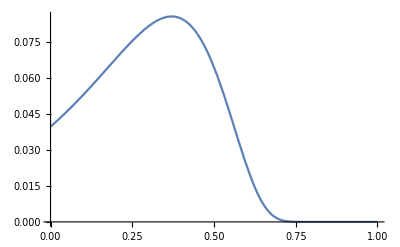

```mathematica
Plot[-(1+x)/(x-1)^3 1/(8 Pi)Exp[-x/(x-1)^2],{x,0,1},PlotRange->All]
```